# Ejercicio I.2: Representación gráfica de una red

## Nombre del Alumno: XXXXXXXXXXXXXXX DNI: xxxxx xxxxxx

```mathematica
Clear["Global`*"]
```

# 1.- Construir grafo de una cola SIMPLE

```mathematica
SetAttributes[createPrimitive,HoldAll]

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
```

```mathematica
a=createPrimitive[face[x_: 0.1],
{Circle[{1.5 x,0},x],Line[{{-x,x},{0,x},{0,-x},{-x,-x}}],Line[{{0,0},{x/2,0}}]
}]
```

```mathematica
MakeBoxes[Interpretation[expr,p]]//DisplayForm
```

expr

```mathematica
InterpretationBox["expr",p]//DisplayForm
```

expr

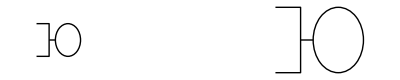

```mathematica
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]]
```

# 2.- Construir una topología gráfica de red

```mathematica
GraphPlot[{1->5,1->2,2->3,2->4,5->2,5->4,4->3},DirectedEdges->True,VertexLabeling->True,]
```

GraphPlot::argx: GraphPlot called with 4 arguments; 1 argument is expected.

GraphPlot[{1→5,1→2,2→3,2→4,5→2,5→4,4→3},DirectedEdges→True,VertexLabeling→True,Null]

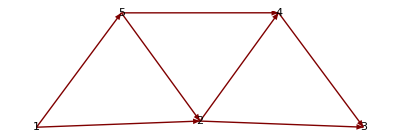

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
arrow=Graphics[face[0.01]];
```

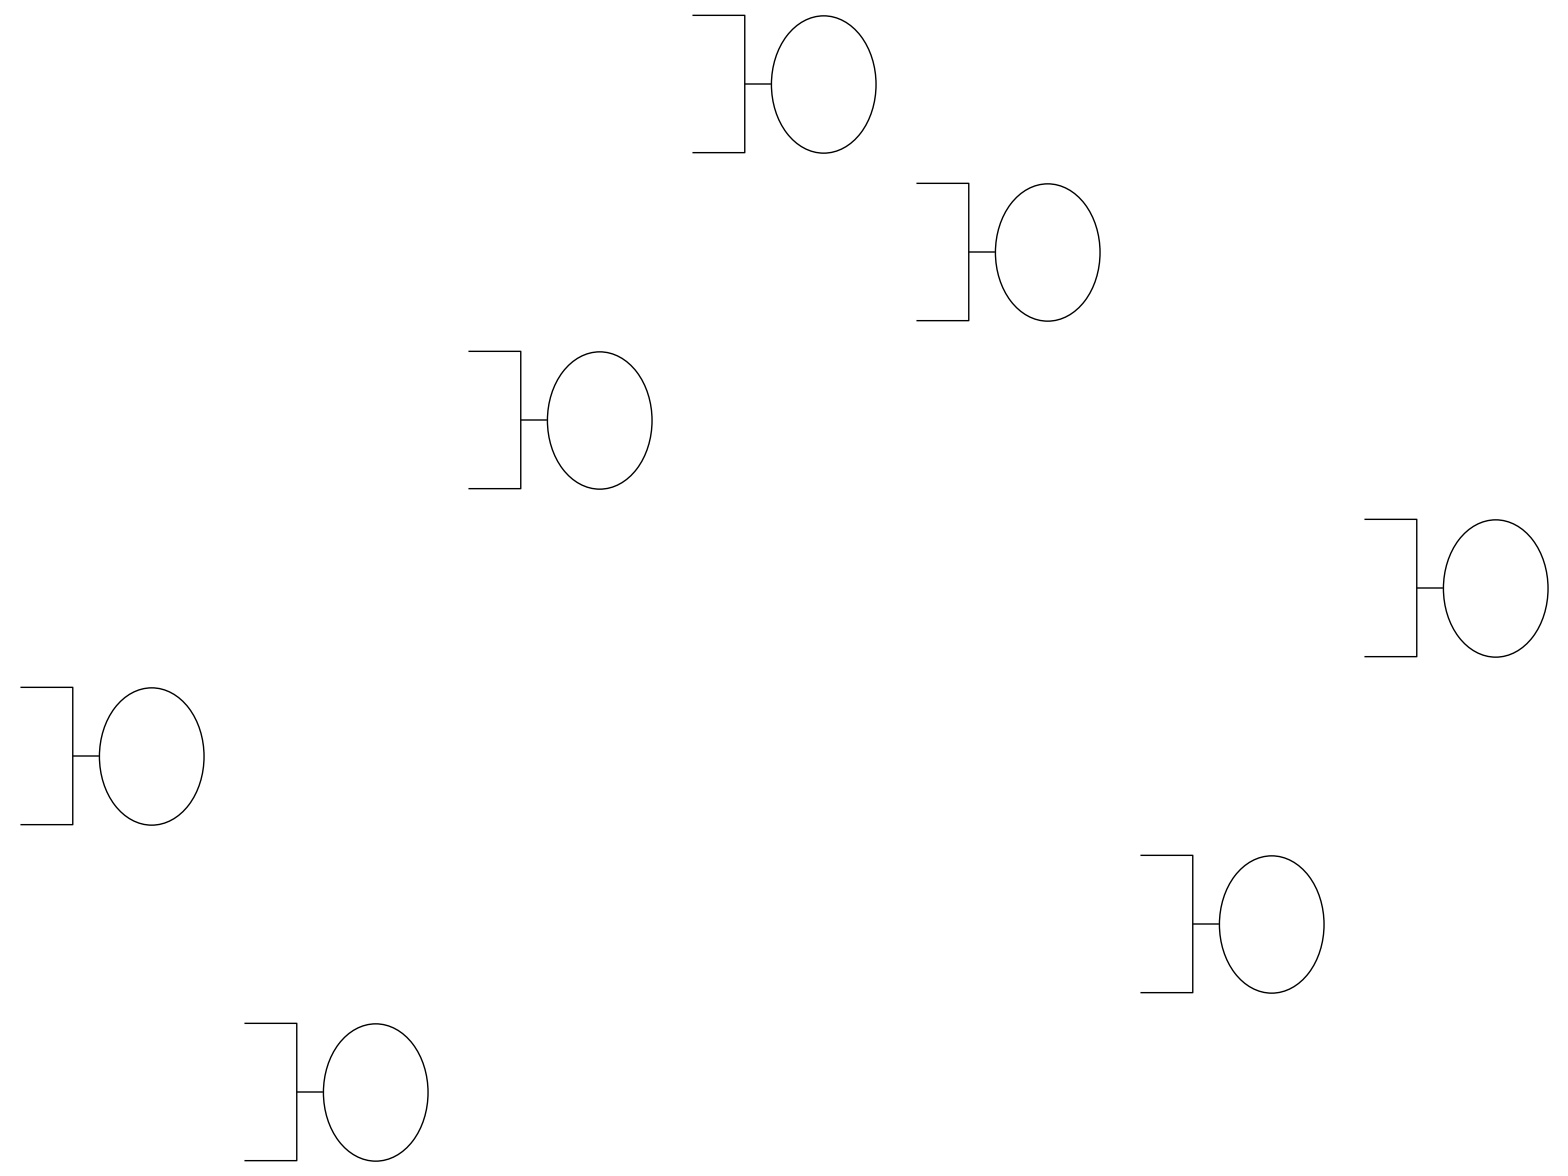

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4},DirectedEdges->True,VertexLabeling->True,EdgeRenderingFunction->({Line[#],Inset[arrow,Mean[#1],Automatic,0.3,#[[2]]-#[[1]],Background->White]}&)]
```

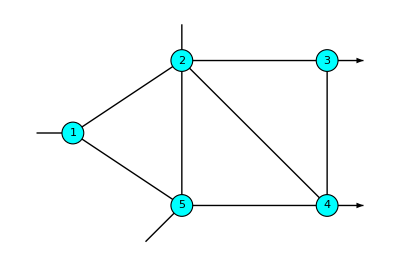
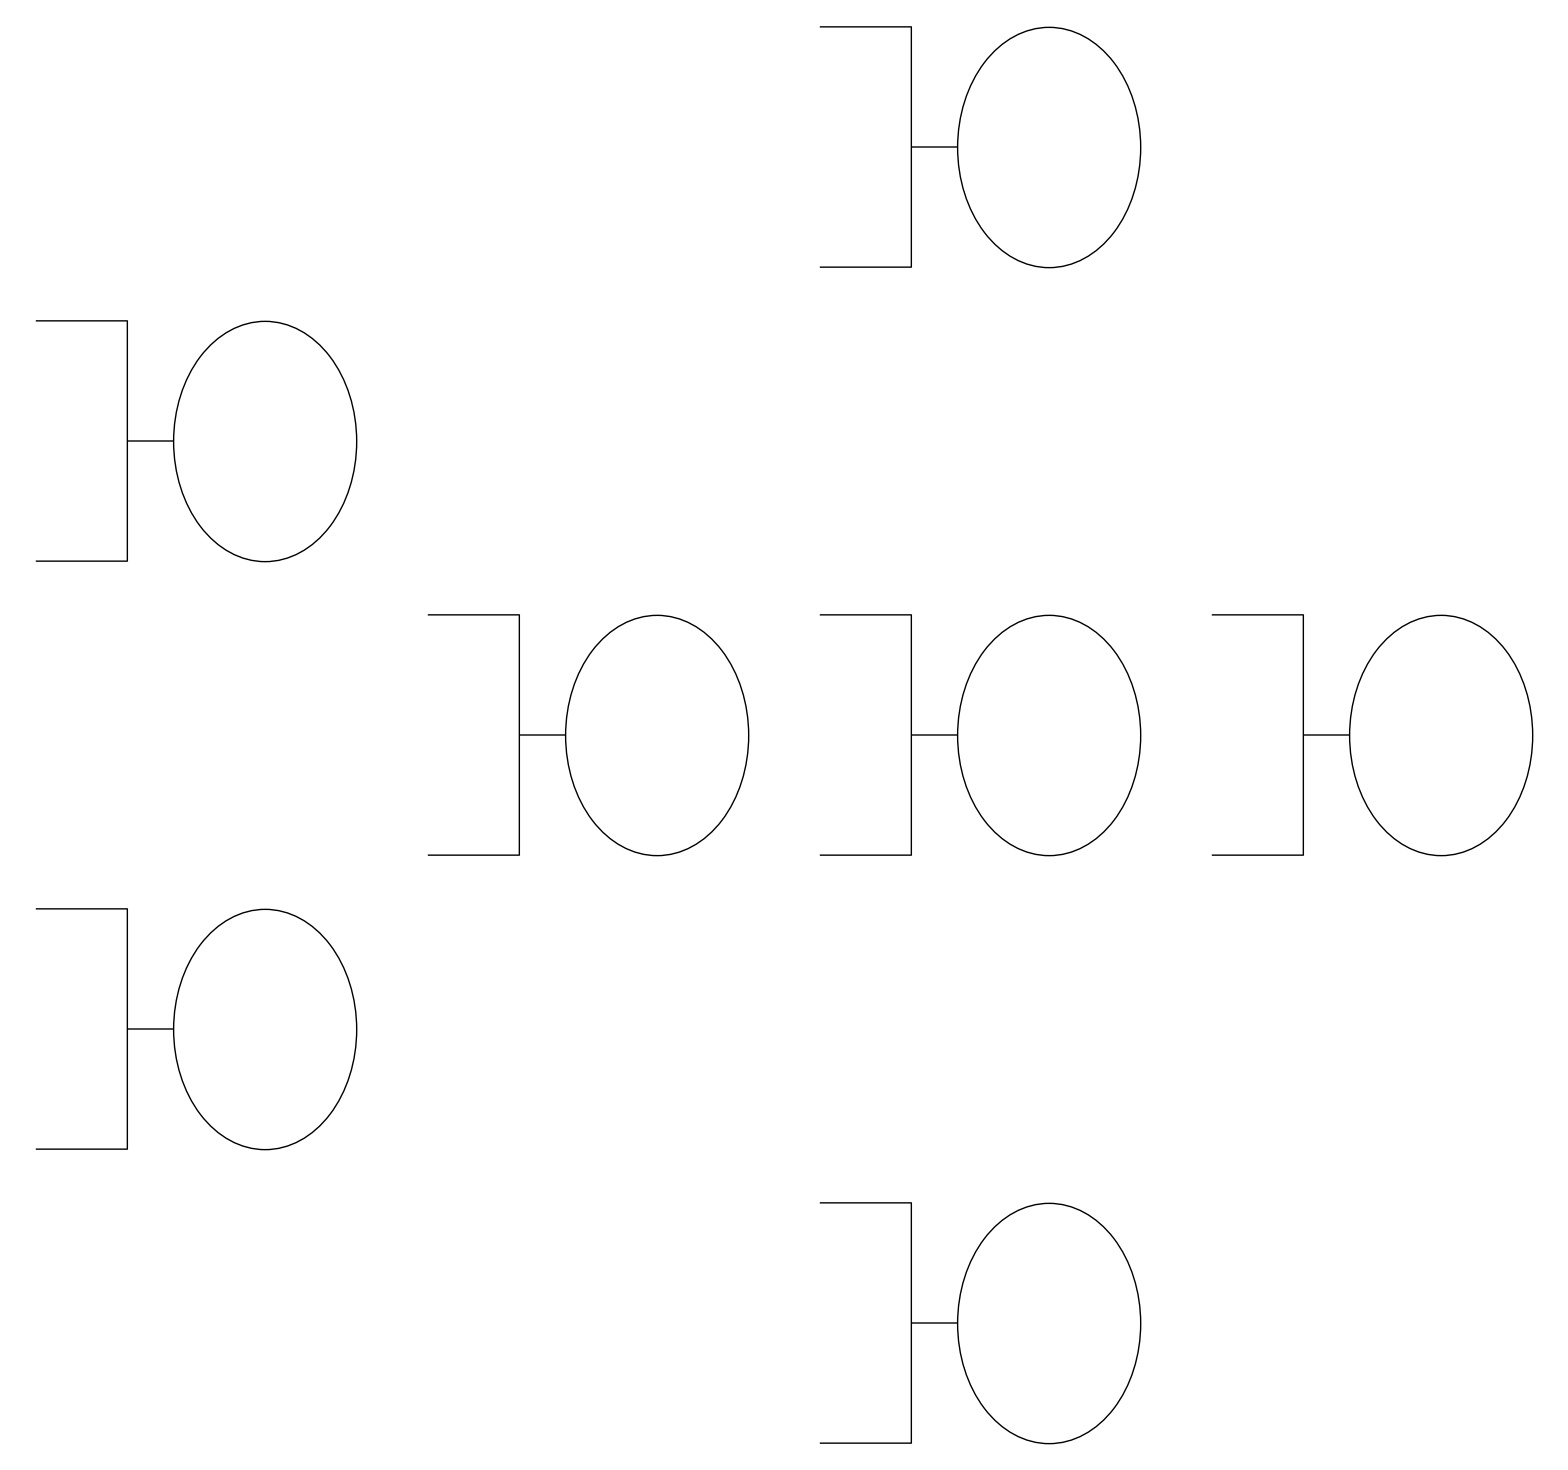

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

# 3.- Adaptar la topología de red física a una red de colas equivalente

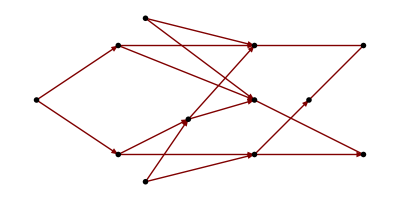

```mathematica
GraphPlot[{{{1,5}->{5,2},"1/2"},{{1,5}->{5,4},"1/2"},{{1,2}->{2,3},"1/3"},{{1,2}->{2,4},"2/3"},{{5,2}->{2,3},"1/3"},{{5,2}->{2,4},"2/3"},{{2,2}->{2,3},"1/3"},{{2,2}->{2,4},"2/3"},{{1,1}->{1,2},"1/4"},{{1,1}->{1,5},"3/4"},{{5,5}->{5,2},"1/2"},{{5,5}->{5,4},"1/2"},{2,4}->{4,4},{{5,4}->{4,4},"1"},{2,3}->{3,3},{{5,4}->{4,3},"0"},{4,3}->{3,3}},

VertexCoordinateRules->{{1,1}->{0,0},{1,2}->{1.5,1},{1,5}->{1.5,-1},{2,4}->{4,0},{5,5}->{2,-1.5},{2,3}->{4,1},{5,4}->{4,-1},{3,3}->{6,1},{4,4}->{6,-1},{2,2}->{2,1.5},{4,3}->{5,0}},VertexRenderingFunction-> ({Inset[arrow,#,Automatic,If[#2[[1]]==#2[[2]],0.2,0.5],If[#2=={5,2},{1,0.8},If[#2=={2,4},{2,-1},If[#2=={4,3},{1,1},{1,0}]]],Background->White]}&)
]
```